```mathematica
Row@Table[SphericalPlot3D[SphericalHarmonicY[l,0,θ,ϕ],{θ,0,Pi},{ϕ,0,2Pi},PlotLabel->Subscript[Y, l]^0,Axes->None,Boxed->False,ImageSize->100,Mesh->False,PlotRange->All],{l,0,10}]
```

-Graphics3D--Graphics3D--Graphics3D--Graphics3D--Graphics3D--Graphics3D--Graphics3D--Graphics3D--Graphics3D--Graphics3D--Graphics3D-

Table::nliter: Non-list iterator {l,0,10} {m,0,1} at position 2 does not evaluate to a real numeric value.

```mathematica
Y[l_,m_] := SphericalHarmonicY[l,m,θ,ϕ]
Ybar[l_,m_] := SphericalHarmonicY[l,-m,θ,ϕ] 
 P[l_,m_] :=Y[l,m]*Ybar[l,m]

SphericalPlot3D[Evaluate[P[4,4],{θ,0,Pi}],{ϕ,0,2Pi},Boxed->False,Axes->None]
```

-Graphics3D-

```mathematica
Y[l_,m_] := SphericalHarmonicY[l,m,θ,ϕ]
Ybar[l_,m_] := SphericalHarmonicY[l,-m,θ,ϕ] 
 P[l_,m_] :=Y[l,m]*Ybar[l,m]
GraphicsGrid[Table[SphericalPlot3D[Evaluate[P[l,m],{θ,0,Pi}],{ϕ,0,2Pi},Boxed->False,PlotLabel->Subscript[Y, l]^m,Axes->None],{l,0,2},{m,0,2}]]
```

-Graphics-

```mathematica
(*Parametri del moto elicoidale*)raggio=2;
velAngolare=2; (*Velocità angolare*)
velLineare=0.5; (*Velocità lineare lungo z*)
tempoTotale=10; (*Tempo totale*)
numPunti=1000; (*Numero di punti per il grafico*)

(*Calcolo delle coordinate del moto elicoidale*)
t=Subdivide[0,tempoTotale,numPunti];
x=raggio Cos[velAngolare t];
y=raggio Sin[velAngolare t];
z=velLineare t;

(*Grafico del moto elicoidale*)
helix=Graphics3D[Line[Transpose[{x,y,z}]],Boxed->False,Axes->False,AxesLabel->{"x","y","z"}];

(*Visualizzazione*)
Show[helix]
```

-Graphics3D-

10

1.05×10^-34

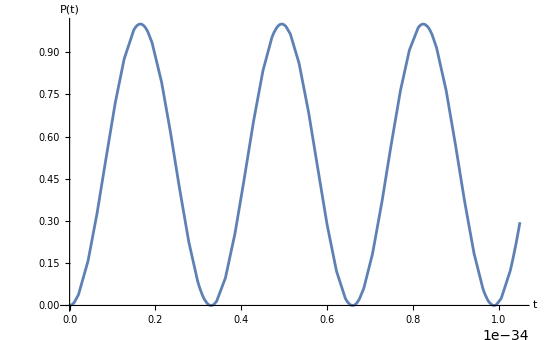

```mathematica
A = 10
h = 1.05*10^-34
f[t_]:= Sin[ A *t/h]^2
Plot[Sin[ A *t/h]^2,{t,0,h}, AxesLabel->{"t","P(t)"}]
```

```mathematica
Plot[(x^2-2)^2,{x,-4,4},PlotRange->{{-4,4},{0,10}},AxesLabel->{"x","V"}]
```

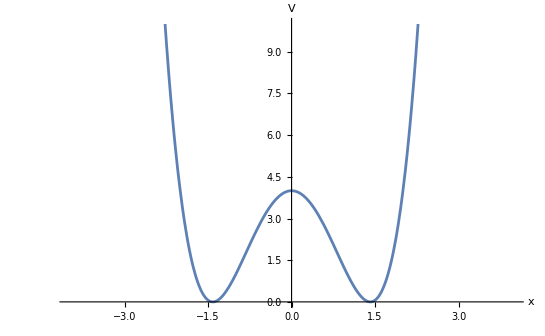

```mathematica
MoleculePlot3D[NH3]
```

MoleculePlot3D::mol: Argument NH3 is not a valid molecule.

```mathematica
MoleculePlot3D["ammonia",Axes->True,AxesLabel->{"x","y","z"},AtomLabels->Thread[Placed[{"N","H","H","H"},Center]]]
```

-Graphics3D-

```mathematica
MoleculePlot3D["ammonia",Axes->True,AxesLabel->{"x","y","z"},AtomLabels->Thread[Placed[{"N","H","H","H"},Center]]]
```

-Graphics3D-

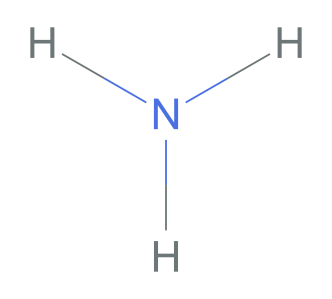

```mathematica
MoleculePlot["ammonia"]
```

```mathematica
MoleculePlot3D["benzene",AtomLabels->Thread[Placed[{"C","C","C","C","C","C","H","H","H","H","H","H"},Center]]]
```

```mathematica
a =2
f1[x_]:= Sqrt[1/2a]Sin[(x Pi)/a]
```

2

```mathematica
1
```

1

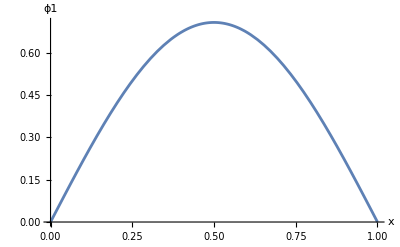

```mathematica
plot1 = Plot[f1[x],{x,0,1},AxesLabel->{x,ϕ1}]
```

```mathematica
f2[x_]:= Sqrt[1/2a]Sin[(x 2Pi)]
```

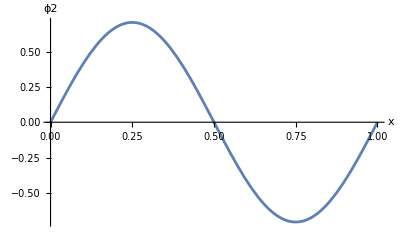

```mathematica
plot2 = Plot[f2[x],{x,0,1},AxesLabel->{x,ϕ2}]
```

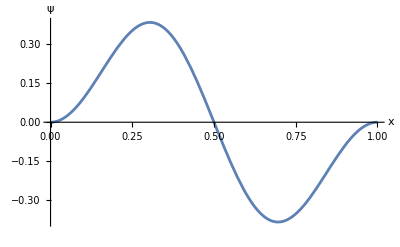

```mathematica
f3[x_]:= (1/2a)Sin[(x 2Pi)]Sin[(x Pi)/a]
plot3 = Plot[f3[x],{x,0,1},AxesLabel->{x,ψ}]
```

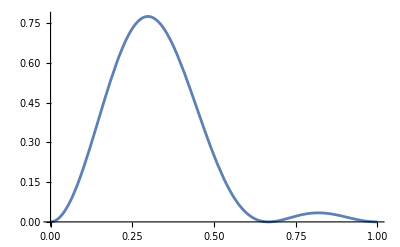

```mathematica
f4[x_] := Abs[f1[x]]^2/2 + Abs[f2[x]]^2/2 + f3[x]
plot4 = Plot[f4[x],{x,0,1}]
```

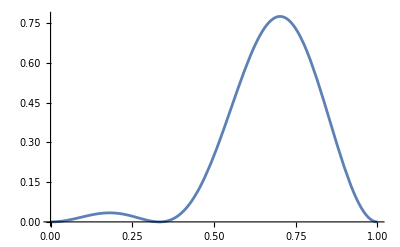

```mathematica
f5[x_]:= Abs[f1[x]]^2/2 + Abs[f2[x]]^2/2 -f3[x]
plot5 = Plot[f5[x],{x,0,1}]
```

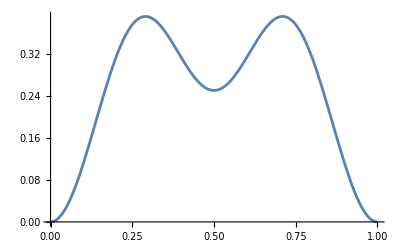

```mathematica
f6[x_] :=  Abs[f1[x]]^2/2 + Abs[f2[x]]^2/2
plot6 = Plot[f6[x],{x,0,1}]
```

```mathematica
GraphicsGrid[{{plot1,plot2,plot3}},Frame->All,ImageSize->800]
```

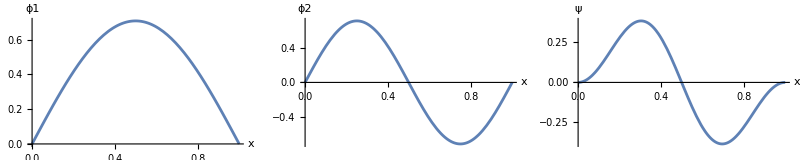

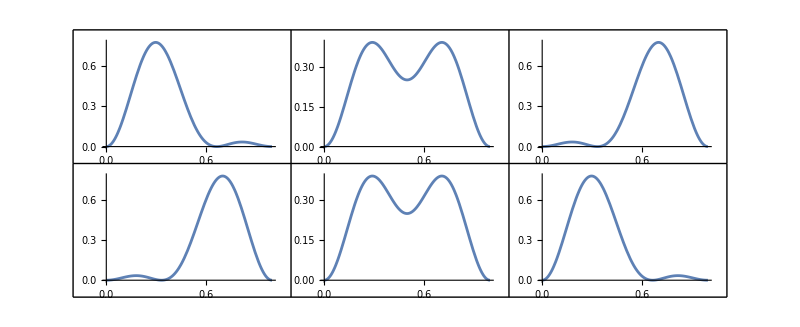

```mathematica
GraphicsGrid[{{plot4,plot6,plot5},{plot5,plot6,plot4}},Frame->All,ImageSize->800]
```

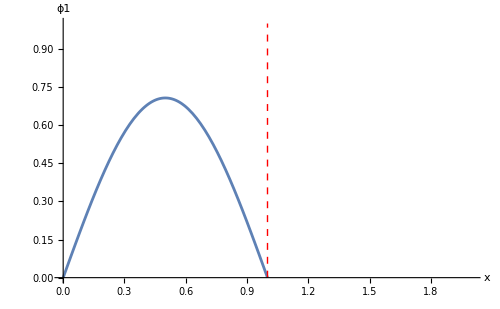

```mathematica
Plot[f1[x],{x,0,1},AxesLabel->{x,ϕ1}, PlotRange->{{0,2},{0,1}},Epilog->{Dashed,Red,Line[{{1,0},{1,1}}]},ImageSize->500]
```

```mathematica
Plot[f1[x],{x,0,2},AxesLabel->{x,ϕ1}, ImageSize->300]
```

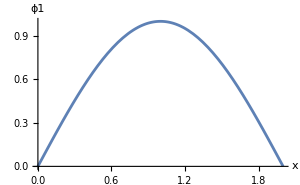

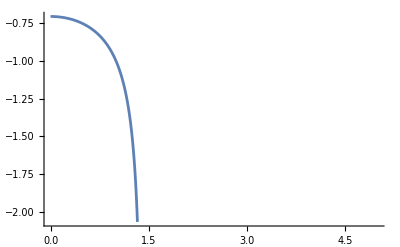

```mathematica
k[x_]:= -1/Sqrt[2-x^2]
g[x_] := Tan[x]

plt1 = Plot[k[x],{x,0,5}]
plt2 = Plot[g[x],{x,0,5}]
```

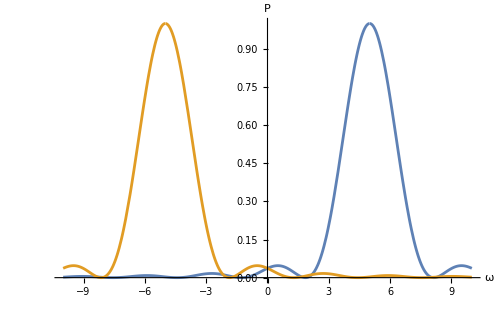

```mathematica
Plot[{Sin[x-5]^2/(x-5)^2,Sin[x+5]^2/(x+5)^2},{x,-10,10},ImageSize -> 500,AxesLabel->{Style["ω",FontSize->14],Style["P",FontSize->14]} ,PlotLegends->{"ω"}]
```